```mathematica
mub[s_]:=1307.5/(1+0.288*s)
```

```mathematica
mub[200]
```

22.3123

```mathematica
mub[62.4]
```

68.9203

```mathematica
mub[54.4]
```

78.4475

```mathematica
mub[39]
```

106.892

```mathematica
mub[27]
```

148.986

```mathematica
mub[19.6]
```

196.77

```mathematica
mub[14.5]
```

252.608

```mathematica
mub[11.5]
```

303.224

```mathematica
mub[7.7]
```

406.359

```mathematica
tc[s_]:=158.4/(1+Exp[2.60-Log[s]/0.45])
```

```mathematica
tc[200]
```

158.384

```mathematica
tc[62.4]
```

158.182

```mathematica
tc[54.4]
```

158.104

```mathematica
tc[39]
```

157.781

```mathematica
tc[27]
```

157.006

```mathematica
tc[19.6]
```

155.585

```mathematica
tc[14.5]
```

152.992

```mathematica
tc[11.5]
```

149.552

```mathematica
tc[7.7]
```

138.428

```mathematica
Tf4={{mub[200],tc[200]},{mub[62.4],tc[62.4]},{mub[54.4],tc[54.4]},{mub[39],tc[39]},{mub[27],tc[27]},{mub[19.6],tc[19.6]},{mub[14.5],tc[14.5]},{mub[11.5],tc[11.5]},{mub[7.7],tc[7.7]}}
```

{{22.3123,158.384},{68.9203,158.182},{78.4475,158.104},{106.892,157.781},{148.986,157.006},{196.77,155.585},{252.608,152.992},{303.224,149.552},{406.359,138.428}}

```mathematica
mub1={0.7,24,34,74,230,275,380,430,580}
```

{0.7,24,34,74,230,275,380,430,580}

```mathematica
Tf={156.5,156.5,151.8,140.4,128.8,124.2,113.9,107.3,80.9}
```

{156.5,156.5,151.8,140.4,128.8,124.2,113.9,107.3,80.9}

```mathematica
a=Transpose[{mub1,Tf}]
```

{{0.7,156.5},{24,156.5},{34,151.8},{74,140.4},{230,128.8},{275,124.2},{380,113.9},{430,107.3},{580,80.9}}

```mathematica
f=Interpolation[Transpose[{mub1,Tf}],Method->"Spline"]
```

InterpolatingFunction[{{0.7, 580.}}, <>]

ListPlot::lpn: InterpolatingFunction[{{0.7,580.}},{5,39,0,{9},{4},0,0,0,0,Automatic,{},{},False},{{0.7,24.,34.,74.,230.,275.,380.,430.,580.}},{BSplineFunction[{{0.7,580.}},<>],{}},{Automatic}][x] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

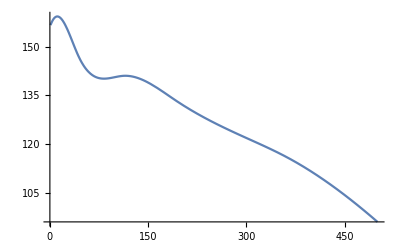
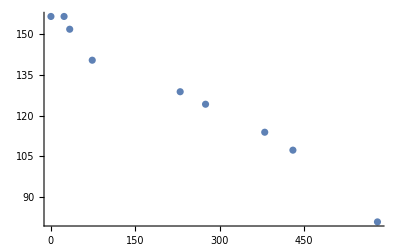
Show[-Graphics-,-Graphics-,ListPlot[InterpolatingFunction[{{0.7, 580.}}, <>][x]]]

```mathematica
Show[Plot[f[x],{x,1,500}],ListPlot[a],ListPlot[f[x]]]
```

```mathematica
f[22.312286689419796]
f[68.92025807539851]
f[78.44748968033025]
f[106.89175931981688]
f[148.985870556062]
f[196.77040693474598]
f[252.60819165378675]
f[303.22356215213364]
f[406.358776727996]
```

157.147

140.787

140.227

140.928

139.075

132.829

126.395

121.593

110.586

```mathematica
Clear[f3]
```

```mathematica
TFc=Import[NotebookDirectory[]<>"/Tf3/Tcf.dat"]
```

{{2.70036,63.3898},{3.32045,73.5593},{3.81107,85.7627},{4.32424,93.8983},{4.85049,126.102},{6.31682,130.169},{7.67868,137.966},{8.81327,147.797},{17.3541,153.898},{62.8066,163.051},{130.981,161.017},{198.042,162.034},{2747.28,156.271}}

```mathematica
mubc=Import[NotebookDirectory[]<>"/Tf3/muB.dat"]
```

{{2.73155,758.416},{3.32045,667.327},{3.81107,609.901},{4.32424,576.238},{4.85049,546.535},{6.31682,429.703},{7.41864,378.218},{12.2963,275.248},{17.3541,229.703},{62.8066,75.2475},{130.981,35.6436},{200.33,23.7624},{2747.28,0.}}

```mathematica
Tmub=Table[{mubc[[i,2]],TFc[[i,2]]},{i,1,13}]
```

{{758.416,63.3898},{667.327,73.5593},{609.901,85.7627},{576.238,93.8983},{546.535,126.102},{429.703,130.169},{378.218,137.966},{275.248,147.797},{229.703,153.898},{75.2475,163.051},{35.6436,161.017},{23.7624,162.034},{0.,156.271}}

```mathematica
f2=Interpolation[TFc,Method->"Spline",InterpolationOrder->1]
f3=Interpolation[Tmub,Method->"Spline",InterpolationOrder->1]
f5=Interpolation[Tmub,Method->"Spline",InterpolationOrder->2]
```

InterpolatingFunction[{{2.70036, 2747.28}}, <>]

InterpolatingFunction[{{0., 758.416}}, <>]

InterpolatingFunction[{{0., 758.416}}, <>]

```mathematica
exp={{7.7,f2[7.7]},{11.5,f2[11.5]},{14.5,f2[14.5]},{19.6,f2[19.6]},{27,f2[27]},{39,f2[39]},{54.4,f2[54.4]},{62.4,f2[62.4]},{200,f2[200]}}
```

{{7.7,138.151},{11.5,149.716},{14.5,151.859},{19.6,154.351},{27,155.841},{39,158.257},{54.4,161.358},{62.4,162.969},{200,162.029}}

```mathematica
s={200,62.4,54.4,39,27,19.6,14.5,11.5,7.7}
```

{200,62.4,54.4,39,27,19.6,14.5,11.5,7.7}

```mathematica
mub2={22.312286689419796,68.92025807539851,78.44748968033025,106.89175931981688,148.985870556062,196.77040693474598,252.60819165378675,303.22356215213364,406.358776727996}
```

{22.3123,68.9203,78.4475,106.892,148.986,196.77,252.608,303.224,406.359}

```mathematica
Tf2=Table[{mub2[[i]],f2[s[[i]]]},{i,1,9}]
```

{{22.3123,162.029},{68.9203,162.969},{78.4475,161.358},{106.892,158.257},{148.986,155.841},{196.77,154.351},{252.608,151.859},{303.224,149.716},{406.359,138.151}}

```mathematica
Tf3=Table[{mub2[[i]],f3[mub2[[i]]]},{i,1,9}]
```

{{22.3123,161.682},{68.9203,162.726},{78.4475,162.861},{106.892,161.176},{148.986,158.681},{196.77,155.85},{252.608,150.83},{303.224,145.126},{406.359,133.705}}

```mathematica
Tf5=Table[{mub2[[i]],f5[mub2[[i]]]},{i,1,9}]
```

{{22.3123,162.021},{68.9203,162.585},{78.4475,163.256},{106.892,164.184},{148.986,162.597},{196.77,157.904},{252.608,150.743},{303.224,145.027},{406.359,132.668}}

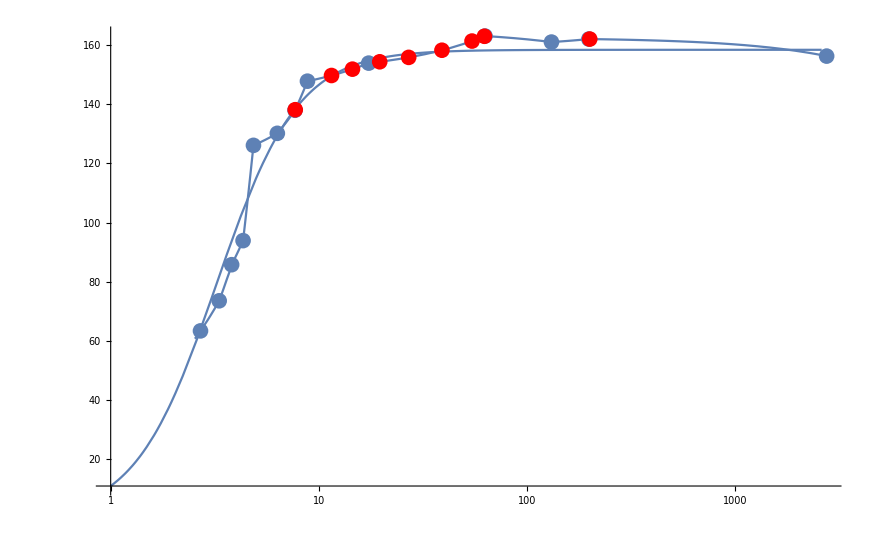

```mathematica
Show[LogLinearPlot[tc[x],{x,1,2600},PlotRange->All],LogLinearPlot[f2[x],{x,0,2600},PlotRange->All],ListLogLinearPlot[TFc,PlotRange->All],ListLogLinearPlot[exp,PlotRange->All,PlotStyle->Red]]
```

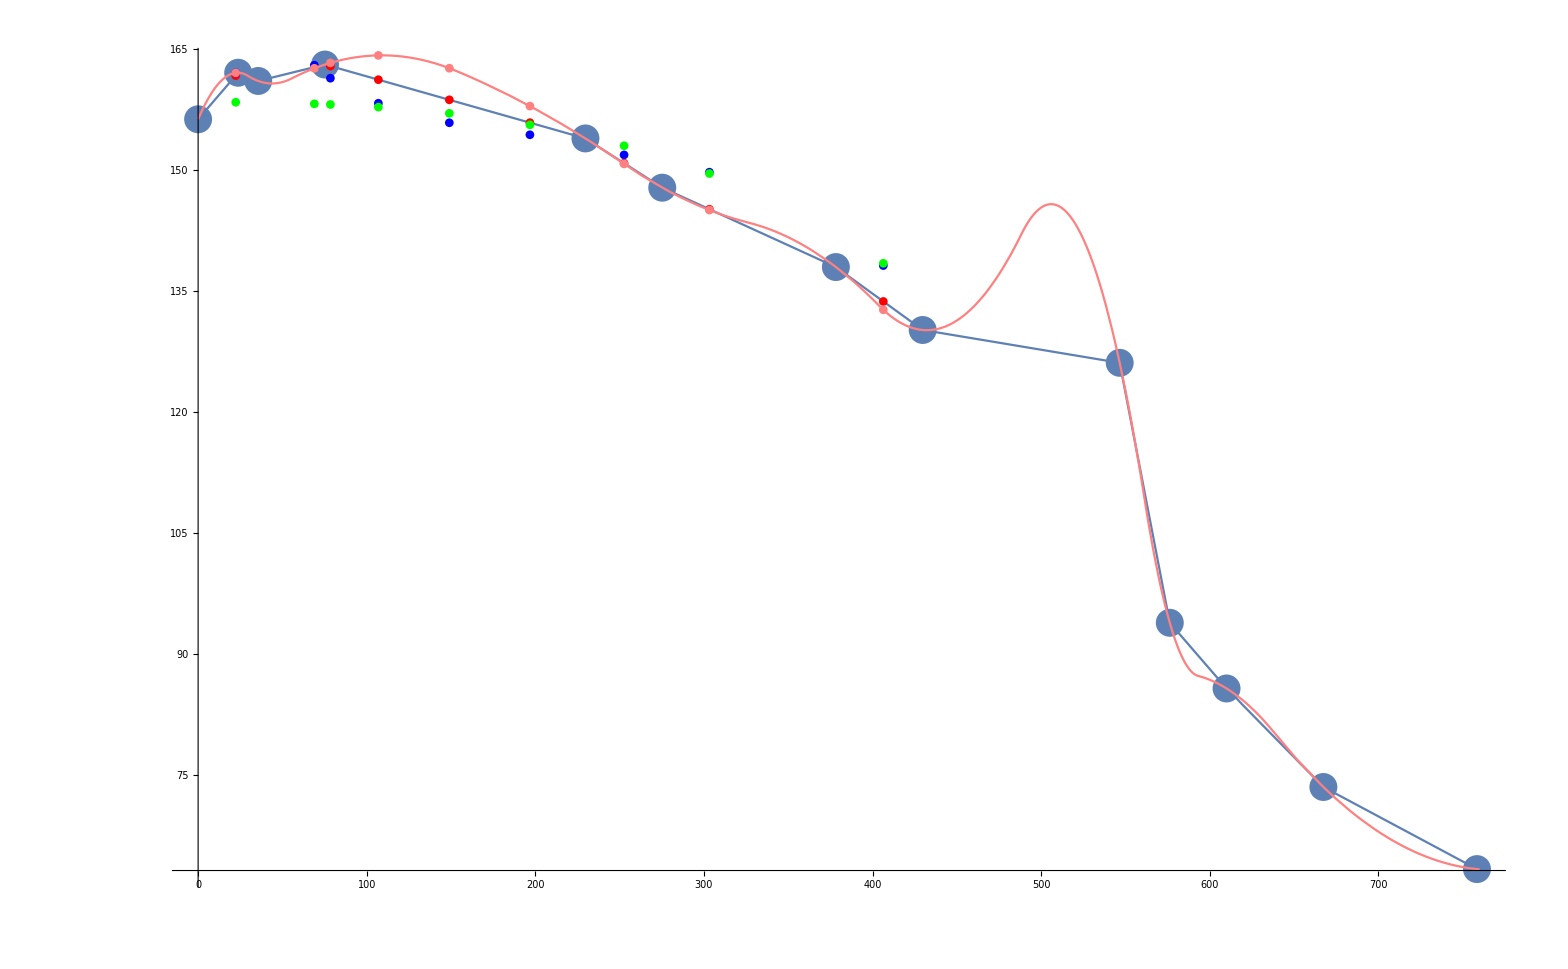

```mathematica
Show[Plot[f3[x],{x,0,760}],ListPlot[Tmub,PlotRange->All],ListPlot[Tf3,PlotStyle->Red,PlotMarkers->Automatic],ListPlot[Tf2,PlotStyle->Blue,PlotMarkers->Automatic],
ListPlot[Tf4,PlotStyle->Green,PlotMarkers->Automatic],Plot[f5[x],{x,0,760},PlotStyle->Pink],ListPlot[Tf5,PlotStyle->Pink,PlotMarkers->Automatic]]
```

```mathematica
f3[mub2]
```

{161.682,162.726,162.861,161.176,158.681,155.85,150.83,145.126,133.705}

```mathematica
exp={{200,f2[200]},{62.4,f2[62.4]},{54.4,f2[54.4]},{39,f2[39]},{27,f2[27]},{19.6,f2[19.6]},{14.5,f2[14.5]},{11.5,f2[11.5]},{7.7,f2[7.7]}}
```

{{200,162.029},{62.4,162.969},{54.4,161.358},{39,158.257},{27,155.841},{19.6,154.351},{14.5,151.859},{11.5,149.716},{7.7,138.151}}